Temperature Response Function

## Setup

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

## Sigmoidal response function

```mathematica
fmax=5;
tempThresh=2.5;
omegaVals={1,1.5,3,10};
```

```mathematica
Clear[resSig]
resSig[temp_,omega_]:=fmax/(1+Exp[-omega(temp-tempThresh)]);
```

```mathematica
legendOmega=LineLegend[Table[TMBcolours[[i]],{i,Length[omegaVals]}],Table["ω="<>ToString[omegaVals[[i]]],{i,Length[omegaVals]}],LabelStyle->12];
```

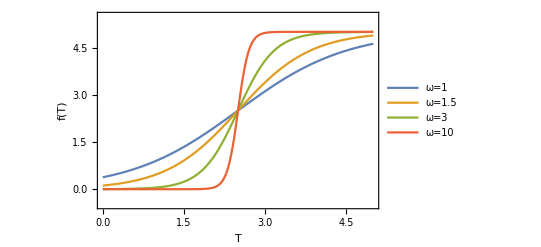

```mathematica
tempResponsePlot=Plot[Evaluate[Table[resSig[temp,omega],{omega,omegaVals}]],{temp,0,5},
LabelStyle->14,
Frame->True,
FrameLabel->{{"f(T)",""},{"T",""}},
PlotRange->{{0,5},{-0.5,fmax+0.5}},
PlotLegends->Placed[legendOmega,Scaled[{0.17,0.7}]]]
```

```mathematica
Export["figures/tempResponsePlot.png",tempResponsePlot,ImageResolution->100];
```

## Manipulate function

```mathematica
Clear[resSigManip]
resSigManip[temp_,omega_,tempThresh_]:=fmax/(1+Exp[-omega(temp-tempThresh)]);
```

```mathematica
Manipulate[Plot[resSigManip[temp,omega,tempThresh],{temp,0,5},
LabelStyle->14,
Frame->True,
FrameLabel->{{"f(T)",""},{"T",""}},
PlotRange->{{0,5},{-0.5,fmax+0.5}}],{{omega,3},0.5,10},{{tempThresh,2.5},1,5}]
```